31 March 2021

# Point Spread Functions for Rectangular and Circular Apertures

## Melvin Friedman

### Introduction

This document describes how to calculate the point spread function (psf) for rectangular and circular apertures subject to the assumption that the psf is determined by the incoherent diffraction limit.  The calculation is done for quasi monochromatic radiation with wavelength λ and the psf is formed by a lens with focal length f.

### Rectangular Aperture

The square aperture has  length 𝕃 and width 𝕎.  The aperture 𝔸 is defined by

	𝔸[x,y]=1/(𝕎 𝕃) rect[x/𝕎] rect[y/𝕃]

where the area of the aperture has been normalized to one.  The Fourier transform of the aperture 𝔸[x,y] gives the amplitude 𝒜 of the disturbance at the focal plane in units of spatial frequency

	ℱ{𝔸[x,y] }=𝒜[ξ , η] =sinc[𝕎 ξ] sinc[𝕃 𝓃]

As explained in the text, the amplitude 𝒜[ξ , η] is converted to spatial coordinates x,y in the focal plane by using the transformation ξ→x/(λ f) , η→ y/(λ f) 

	𝒜[x,y] = 𝒜[ξ,η]/. {ξ→x/(λ f), η→ y/(λ f)} = sinc[𝕎/(λ f)x] sinc[𝕃/(λ f)y]

The psf is the square of 𝒜[x,y]

	(psf =(|𝒜[x,y] |)^2= sinc[𝕎/(λ f)x],𝕃/(λ f)y])^2

where x and y are coordinates in the focal plane, measured from the optical axis,  in directions parallel to the width and length of the aperture.   Define dimensionless quantities 𝕏 and 𝕐

	𝕏= (𝕎 x)/(λ f);       𝕐=(𝕃 y)/(λ f)

The psf is then expressed in terms of 𝕏 and 𝕐

	psf = sinc[𝕏,𝕐]^2

By graphing the psf in terms of dimensionless parameters we get universal graphs of how psf varies with rectangular aperture dimensions.  To get a feel for the size of the psf, instead graph the psf for a square aperture where 𝕎=𝕃=1 mm, f=50 mm, λ=5 μ = 5 10^-3 mm.  Then

```mathematica
𝕎/(λ f)/. {𝕎-> 1, f-> 50, λ-> 5 10^-3}
```

4

The psf is

	psf = sinc[4x,4y]^2

where x and y  are coordinates in the focal plane.

Graph the psf for a square aperture.

```mathematica
psf[x_,y_]:= sinc[4x,4y]^2  (* Define psf in Mathematica *)
```

Graph the psf so as to show the peak of the psf.

```mathematica
g1 =Plot3D[psf[x,y],{x,-1,1},{y,-1,1}, PlotRange-> All, PlotPoints-> 200, PlotLabel-> "Full Scale=1", AxesLabel->{"x [mm]","y [mm]"}]
```

-Graphics3D-

From this figure we see that the central spot has a square shape but is most intense at the center.  Side lobes are barely visible along the x and y axes.

Graph the psf so that side lobes are visible.

```mathematica
g2=Plot3D[psf[x,y],{x,-1,1},{y,-1,1}, PlotRange-> {{-1,1},{-1,1},{0,.1}},PlotPoints-> 200, PlotLabel-> "Full Scale = 0.1", AxesLabel->{"x [mm]","y [mm]"}]
```

-Graphics3D-

In this figure the central peak has been truncated but side lobes along the x and y axes are clearly visible.

Graph the psf so off-axis side lobes are barely visible.

```mathematica
g3=Plot3D[psf[x,y],{x,-1,1},{y,-1,1}, PlotRange-> {{-1,1},{-1,1},{0,.01}},PlotPoints-> 200, PlotLabel-> "Full Scale = 0.01", AxesLabel->{"x [mm]","y [mm]"}]
```

-Graphics3D-

In this figure the side lobes along the x and y axes are almost all truncated but one can now start to see other peaks developing that are not on the x or y axis.

Graph the psf so off-axis side lobes are prominent.

```mathematica
g4=Plot3D[psf[x,y],{x,-1,1},{y,-1,1}, PlotRange-> {{-1,1},{-1,1},{0,.001}},PlotPoints-> 200, PlotLabel-> "Full Scale = 0.001", AxesLabel->{"x [mm]","y [mm]"}]
```

-Graphics3D-

In this figure all the side lobes on the x and y axes are truncated and four off axis peaks are also truncated but off axis peaks that were not visible in the previous figure are now clearly visible.

##### Summarize the square aperture with a single graphic.

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4}}, ImageSize-> Large, PlotLabel-> "PSF of Square Aperture", Frame-> All]
```

Figure 1.  PSF for a square aperture.  a)The psf for a square aperture is shown at full scale.  The peak is seen at (9,0) which is where the optical axis intersects the flocal plane and lobes along the x and y axes are barely visible.  b) At a scale of 0.1 the central peak in a) has been truncated but one can now  see side lobes along the x and y axes which are stronger the closer they are to the central lobe.  c) At a scale of 0.01, some of the side lobes along the x and y axes are truncated but small lobes off the x and y axes are visible.  d) At a scale of 0.001 all the side lobes along the x and y axes are truncated but side lobes are clearly visible off the x and y axes.

### Circular Aperture

The circular aperture has diameter 𝔻.  The procedure for calculating the incoherent psf is the same as that already illustrated for the rectangular aperture so we go directly to the result.    The psf for a circular aperture

psf[x]=  ((2 J_1(x ))/x)^2

where 
	x=(π ⅅ r)/(λ f)

Realize that x is in a radial direction.

Mathematica Implementation.

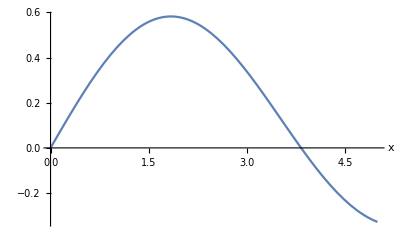

```mathematica
Plot[BesselJ[1,x], {x,0,5}, AxesLabel->Automatic ]
```

Find the first zero of J_1(x)

```mathematica
N[BesselJZero[1,1]]
```

3.83171

```mathematica
psf[x_]:= ((2 BesselJ[1,x])/x)^2 (* Define psf in Mathematica *)
```

Graph psf to show relative strength of central peak and side lobes

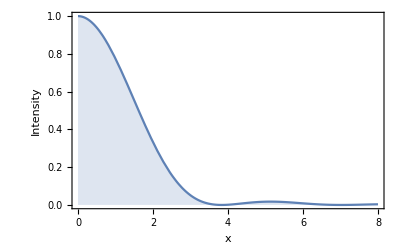

```mathematica
g1 =Plot[psf[x],{x,0,8}, Frame-> True, Filling-> Axis,FrameLabel-> {{"Intensity",""},{"x",""}}]
```

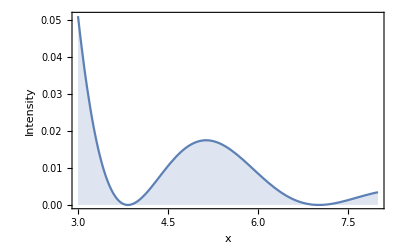

```mathematica
g2=Plot[psf[x], {x,3,8},Frame-> True, Filling-> Axis,FrameLabel-> {{"Intensity",""},{"x",""}}]
```

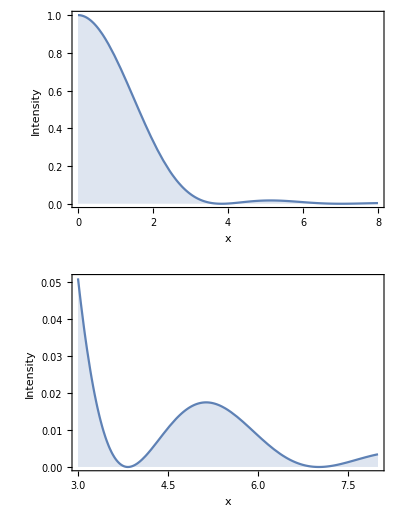

```mathematica
GraphicsGrid[{{g1}, {g2}}, PlotLabel-> "Circular Aperture PSF"]
```

-Graphics-

Figure 2.  PSF for a circular aperture.  Top figure shows the main peak of the psf.  Bottom figure shows there are rings around the main peak but that these rings are of low intensity.

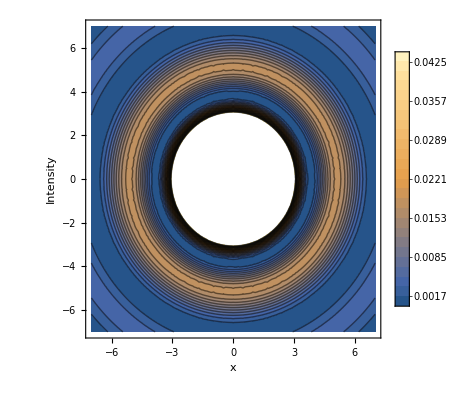

```mathematica
ContourPlot[psf[√(x^2+y^2)], {x,-7,7}, {y,-7,7}, Contours-> 25, PlotPoints-> 30, PlotLegends-> Automatic, FrameLabel-> {{"Intensity",""},{"x","Point Spread Function (Circular Aperture"}}]
```

-Graphics-

Figure 3.  Contour plot of the psf function showing the Airy disc.

Using the observation that the first zero of J_1[x] =3.83  and that x=(πⅅ r)/(λ f) we find that the diameter of the Airy disc d_Airy is given by

	3.83 =(π 𝔻 r)/(λ f)  ⟹ r = (3.83 λ f)/(π 𝔻)     ⟹

d_Airy= 2 r = 7.86/π (λ f)/𝔻=2.44(λ f)/𝔻= 2.44 λ F/# where F/# ≡ f/𝔻